```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## monochromatic

### test

```mathematica
npeak=2^4
```

16

```mathematica
mapdata=Import["data/mono_map_0.dat"][[1]];
```

```mathematica
NL=Length[mapdata]^(1/3)
```

256

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
powerdata=Import["data/mono_power_0.dat"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

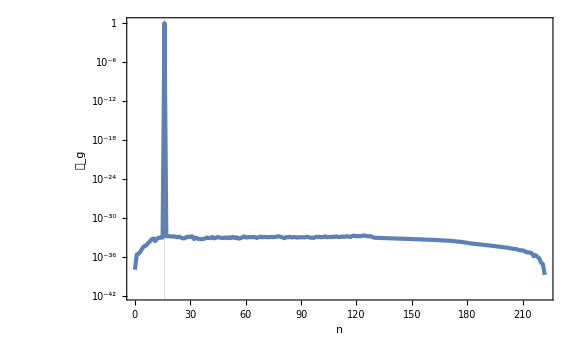

```mathematica
ListLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]}]
```

```mathematica
biasedmap=Import["data/mono_biased_0.dat"][[1]];
lapmap=Import["data/mono_laplacian_0.dat"][[1]];
```

```mathematica
shiftedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

### importance sampling

```mathematica
mukdata=Import["data/mono_muk.dat"];
Ntot=Length[mukdata]
```

1438

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data,ChartLegends->Automatic,FrameLabel->{Subscript[OverTilde[μ], 2],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data,ChartLegends->Automatic,FrameLabel->{Subscript[OverTilde[k], 3],"log_10𝒲"}]
```

-Graphics-

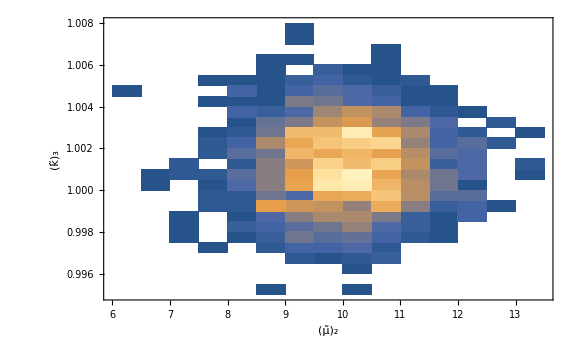

```mathematica
DensityHistogram[mukdata[[All,2;;3]],FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverTilde[k], 3]}]
```

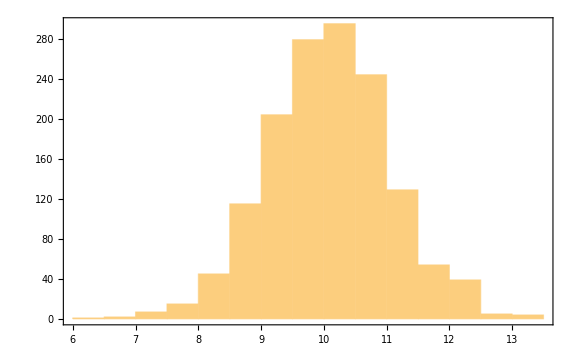

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/2

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

6

27/2

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2-Dmu2/2<=#[[2]]<mu2+Dmu2/2&];
```

```mathematica
PSmu2List=Table[{mu2,Length[mu2binning[mu2]]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

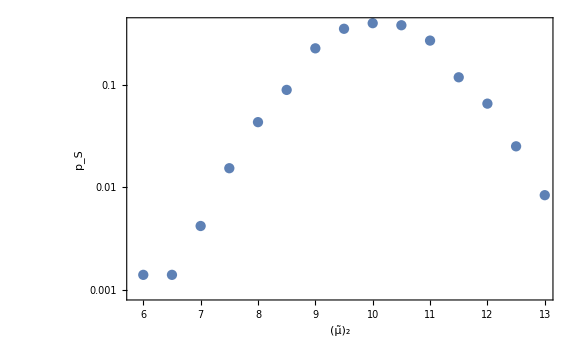

```mathematica
ListLogPlot[PSmu2List,Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

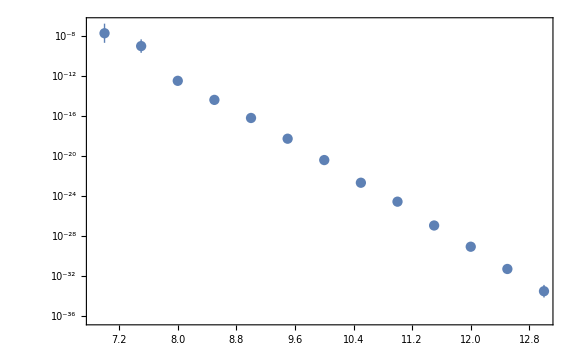

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
PTmu2List=Table[{PSmu2List[[i,1]],PSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[PSmu2List]}];
```

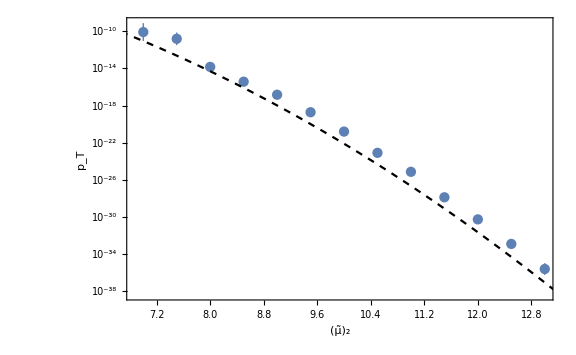

```mathematica
Show[ListLogPlot[PTmu2List,Joined->False,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[p, "T"]}],LogPlot[1/Sqrt[2π] Exp[-x^2/2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
PTmu2List[[9,2]]
1/Sqrt[2π] Exp[-10^2/2]//N
```

1.560.280.3510^-21

7.6946×10^-23

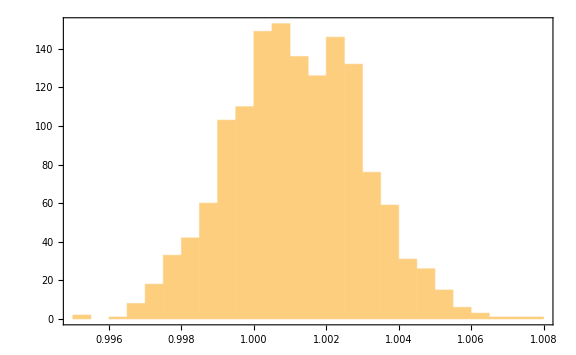

```mathematica
Histogram[mukdata[[All,3]]]
```